```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\李沛然\课程\物理\Particle research\Millicharge_beamdump\sample

```mathematica
testdata=Import["m_e_4GeV\\unweighted_events.lhe","Table"];
```

## Prepare loading

```mathematica
(* Based on the Chameleon package by Philip Shuster, Jesse Thaler, Natalia Toro *)
(* Modified by Maxim Perelstein and Andi Weiler, 2008-09 *)

(*format of the compulsory event vector*)
eventInfo={_,_,_,_,_,_};

ClearAll[particle,finout];

(*PDG numbers see e.g. http://home.fnal.gov/~maeshima/alignment/ORCA/PYTHIA_particle_codes.ps*)

particle[2] ="u";
particle[-2] ="uBar";

particle[1] =d;
particle[-1] =dBar;

particle[3] ="s";
particle[-3] ="sBar";

particle[4] ="c";
particle[-4] ="cBar";

particle[5] =b;
particle[-5] =bBar;

particle[6] =t;
particle[-6] =tBar;

particle[11] =SuperMinus[e];
particle[-11] =SuperPlus[e];

particle[12] ="⋁_e ";
particle[-12] ="(⋁_e)^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="⋁_μ ";
particle[-14] ="(⋁_μ)^c";

particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="⋁_τ ";
particle[-16] ="(⋁_τ)^c";

particle[21] =gluon;

particle[24] ="W^+";
particle[-24] ="W^-";

particle[1000001] =OverTilde[dl];
particle[-1000001] =OverTilde[dl]Bar;





(* *************** *)

particle[23] ="Z";

particle[25] ="h";
particle[35] ="H";

particle[2000001] =OverTilde[dr];
particle[-2000001] =OverTilde[dr]Bar;

particle[1000003] =OverTilde[sl];
particle[-1000003] =OverTilde[sl]Bar;

particle[1000004] =OverTilde[cl];
particle[-1000004] =OverTilde[cl]Bar;



particle[2000003] =OverTilde[sr];
particle[-2000003] =OverTilde[sr]Bar;

particle[2000004] =OverTilde[cr];
particle[-2000004] =OverTilde[cr]Bar;



particle[2000006] =Subscript[OverTilde[t], 2];
particle[-2000006] =SuperStar[Subscript[OverTilde[t], 2]];

particle[1000023] =Subscript[OverTilde[χ], 2];
particle[1000025] =Subscript[OverTilde[χ], 3];
particle[1000035] =Subscript[OverTilde[χ], 4];





(* *************** *)






particle[1000002] =OverTilde[ul];
particle[-1000002] =OverTilde[ul]Bar;
particle[2000002] =OverTilde[ur];
particle[-2000002] =OverTilde[ur]Bar;
particle[1000006] =Subscript[OverTilde[t], 1];
particle[-1000006] =SuperStar[Subscript[OverTilde[t], 1]];
particle[1000022] =Subscript[OverTilde[χ], 1];

particle[1000012] =OverTilde[Subscript[ν, e]];
particle[-1000012] =OverTilde[Subscript[ν, e]]Bar;

particle[1000024]=SuperPlus[x1];
particle[-1000024]=SuperMinus[x1];
particle[1000037] =SuperPlus[x2];
particle[-1000037] =SuperMinus[x2];


particle[1000011] =OverTilde[SuperMinus[el]];
particle[-1000011] =OverTilde[SuperPlus[el]];

particle[2000011] =OverTilde[SuperMinus[er]];
particle[-2000011] =OverTilde[SuperPlus[er]];

particle[1000013] =OverTilde[SuperMinus[μl]];
particle[-1000013] =OverTilde[SuperPlus[μl]];

particle[2000013] =OverTilde[SuperMinus[μr]];
particle[-2000013] =OverTilde[SuperPlus[μr]];

particle[1000015] =Subscript[OverTilde[SuperMinus[τ]], 1];
particle[-1000015] =Subscript[OverTilde[SuperPlus[τ]], 1];

particle[2000015] =Subscript[OverTilde[SuperMinus[τ]], 2];
particle[-2000015] =Subscript[OverTilde[SuperPlus[τ]], 2];




particle[1000021] ="gluino";
particle[1000005] ="OverTilde[bL]";
particle[-1000005] ="OverTilde[bL]bar";
particle[2000005] =OverTilde[br];
particle[-2000005] =OverTilde[br]Bar;


particle[5100002]=du1;
particle[-5100002]=du1Bar;
particle[5100022]=b1;

particle[3333301]=us;
particle[-3333301]=usBar;
particle[3333311]=ux;
particle[-3333311]=uxBar;
particle[3333302]=ns;
particle[3333312]=nx;

particle[9990012]=N1;
particle[9990014]=N2;
particle[9990016]=N3;

finout[-1] = in;
finout[1] = out;
finout[2]  = decayed;

ReadME[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} | eventInfo,2]
);

EventPrint[ event_ ] := ( Print[Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel}}, Table[event⟦i⟧/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13},{i,1,Length[event]}]]//MatrixForm]); 






(*those are input or decayed particles*)
decayedOrIn={_,-1,_,_,_,_,_,_,_,_,_,_,_}|{_,2,_,_,_,_,_,_,_,_,_,_,_};

EventOut[event_]:=(DeleteCases[event,decayedOrIn]);

SetOut[event_]:=(DeleteCases[event,decayedOrIn,2]);




(* Define outgoing objects type *)

(*oJetlhe={2,1,_,_,_,_,_,_,_,_,_,_,_}|{-2,1,_,_,_,_,_,_,_,_,_,_,_}|{21,1,_,_,_,_,_,_,_,_,_,_,_};*)
(* oMissingEnergy={8888,1,_,_,_,_,_,_,_,_,_,_,_};    *)
oElectron = oE=( oEP|oEM);
oElectronMinus= oEM={11,1,___};
oElectronPlus = oEP={-11,1,___};
oMuon = oμ=( oμP|oμM);
oMuonMinus = oμM={13,1,___};
oMuonPlus = oμP={-13,1,___};
oTau = oτ=( oτP|oτM);
oTauMinus = oτM={15,1,___};
oTauPlus = oτP={-15,1,___};
oLeptonMinus  = oLM=(oElectronMinus | oMuonMinus| oTauMinus);
oLeptonPlus  = oLP=(oElectronPlus | oMuonPlus | oTauPlus);
oLepton  = oL=( oLM|oLP);
oPhoton = oγ={22,1,___};
oJet =({21,1,___}|{1,1,___}|{-1,1,___}|{2,1,___}|{-2,1,___}|{3,1,___}|{-3,1,___}|{4,1,___}|{-4,1,___}|{5,1,___}|{-5,1,___});
oB=oBJet=({5,1,___}|{-5,1,___});
oMissingPT = oMPT={12,1,___};
oAny ={_,1,___};
oNot[oType_]:=Except[oType,oAny];




(*EffMassAll[objList_]:=Plus@@Map[ptOf,objList//Transpose,{2}];*)EffMass[event_]:=Plus@@Map[ptOf,event,{1}];
pT[event_]:=Map[ptOf,event,{1}]//Flatten;
eta[event_]:=Map[etaOf,event,{1}]//Flatten;
theta[event_]:=Map[thetaOf,event,{1}]//Flatten;
threeVector[event_]:=Map[ThreeVectorFrom,event,{1}];
(*MissingEnergy[event_]:=Plus@@Map[enOf,event,{1}];*)
ptOf[{_,_,_,_,_,_,px_,py_,___}]:=Sqrt[px^2+py^2];
enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=ArcCos[pz/Sqrt[px^2+py^2+pz^2]];
etaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=-Log[Abs[Tan[ArcCos[pz/Sqrt[px^2+py^2+pz^2]]/2]]];
absetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=Abs[Log[Abs[Tan[ArcCos[pz/Sqrt[px^2+py^2+pz^2]]/2]]]];
abseta[event_]:=Map[absetaOf,event,{1}]//Flatten;

(* ** *)
phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=If[ py≥0,ArcCos[px/Sqrt[px^2+py^2]],2Pi-ArcCos[px/Sqrt[px^2+py^2]]];

phi[event_]:=Map[phiOf,event,{1}]//Flatten;

rapOf[{_,_,_,_,_,_,px_,py_,pz_,En_,___}]:= 1/2 Log[(En+pz)/(En-pz)] ;
rap[event_]:=Map[rapOf,event,{1}]//Flatten;
(* ** *)

FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}]:={En,px,py,pz};
FourLength[{pe_,px_,py_,pz_}]:=Sqrt[pe^2-pz^2-px^2-py^2];

ThreeVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,___}]:={px,py,pz};

CosthetaTwoJet[{jet1_,jet2_}]:=(a=ThreeVectorFrom[jet1];
b=ThreeVectorFrom[jet2];a.b/Sqrt[a.a b.b]);



(* Kinematic quantities for a list of objects  *)
FourVectorSum[objList_]:=Apply[Plus,Map[FourVectorFrom,objList]];
InvMass[objList_] := FourLength[FourVectorSum[objList]];
EffMass[objList_]  := Apply[Plus, Map[ptOf, objList]];

(*MissingPT[objList_]:=If[(NumOf[oMissingPT]~eq~1)[objList],ptOf[HGet[oMissingPT,1][objList]],0];*)

DeltaPhi[obj1_,obj2_]:=Module[{dϕ},dϕ=phiOf[obj1]-phiOf[obj2];
Min[Abs[dϕ],2 π-Abs[dϕ]]];
DeltaPhi[{a_}]:=DeltaPhi[a];
DeltaR[obj1_,obj2_]:=√((etaOf[obj1]-etaOf[obj2])^2+DeltaPhi[obj1,obj2]^2);
DeltaR[{a_}]:=DeltaR[a];

(* Counting objects  *)
NumOf[objType_][objList_]:=Count[objList,objType];

Subscript[M, T][obj1_,obj2_]:= √(2*ptOf[obj1]*ptOf[obj2]*(1-Cos[DeltaPhi[obj1,obj2]])) ;




GetAll[evt_]:=evt;
all[evt_]:=True;
Freq[evtList_,crit_,objsel_,plotfunc_,{min_,max_,nbins_}]:=BinCounts[Flatten[plotfunc/@Flatten4[objsel/@Select[evtList,crit]]],{min,max,(max-min)/nbins}];
Hist[freqcombo__,{min_,max_,nbins_},HistogramOptions___]:=Histogram[freqcombo/.Bin[args__]->Freq[args,{min,max,nbins}],FrequencyData->True,HistogramCategories->Table[i,{i,min,max,(max-min)/nbins}],HistogramOptions];
Flatten4[List_]:=Flatten[List,Max[0,Depth[List]-4]];
PTSort[event_]:=Sort[event,Greater[ptOf[#1],ptOf[#2]]&];
and[f_][evt_]:=f[evt];
and[f_,g__][evt_]:=f[evt]&&and[g][evt];
or[f_][evt_]:=f[evt];
or[f_,g__][evt_]:=f[evt]||or[g][evt];
join[f_][evt_]:=f[evt];
join[f_,g__][evt_]:=f[f[evt],join[g[evt]]];




(* Choose hardest n objects of given type,or a list of objects of given type,indexed by hardness

HGet[patt,n] returns hardest n objects matching patt
HGet[patt,-n] "      softest n     " "           "
HGet[patt,All] returns all objects in an event matching patt
HGet[patt,{k1,k2...,km}] returns k1'th,k2'th,..km'th hardest objects matching patt
HGet[{{patt1,n},{patt2,{k}},{patt3,{-n}}}] joins what you'd get from acting on each pair separately

 *)

HGet[patt_,n_][evt_]:=Take[PTSort[Cases[evt,patt]],n];
HGet[patt_,{n__}][evt_]:=Part[PTSort[Cases[evt,patt]],{n}];
HGet[patt_,All][evt_]:=Cases[evt,patt];
HGet[{{patt1_,sel1_},MoreArgs___}][evt_]:=Join[HGet[patt1,sel1][evt],HGet[{MoreArgs}][evt]];
HGet[patt_,UpTo[n_]][evt_]:=If[Abs[n]<Length[Cases[evt,patt]],Take[PTSort[Cases[evt,patt]],n],Cases[evt,patt]];
HGet[{}][evt_]:=List[];




(* Sorting by any function (can also be used to sort ktuples) *)

FSort[func_][objList_]:=Sort[objList,Greater[func[#1],func[#2]]&];


(* Selection as in HGet but with arbitrary function used for sorting (can also be used on lists of ktuples,with function acting on tuples)  *)

FGet[func_,patt_,n_][evt_]:=Take[FSort[func][Cases[evt,patt]],n];
FGet[func_,patt_,{n__}][evt_]:=Part[FSort[func][Cases[evt,patt]],{n}];
FGet[func_,patt_,All][evt_]:=Cases[evt,patt];
FGet[func_,patt_,UpTo[n_]][evt_]:=If[Abs[n]<Length[Cases[evt,patt]],Take[FSort[func][Cases[evt,patt]],n],Cases[evt,patt]];
FGet[{{func1_,patt1_,sel1_},MoreArgs___}][evt_]:=Join[FGet[func1,patt1,sel1][evt],HGet[{MoreArgs}][evt]];
FGet[{}][evt_]:=List[];
GMM=DiagonalMatrix[{-1,-1,-1,1}];
Invmassf[a_]:=Sqrt[a.GMM.a]
```

## Analysis

```mathematica
eveLLtestdata=ReadME[testdata];(*9999 is mCP, 9912 is nuclei*)(* 7,8,9,10 are px,py,pz,E *)
```

#### show some example

```mathematica
eveLLtestdata[[10]] (* 10th event (total 50k events) *)
eveLLtestdata[[100]] (*100th event*)
eveLLtestdata[[10,-1]] (*For the 10th event, pick the last particle*)
eveLLtestdata[[10,-1,7]] (*px*)
etaOf[eveLLtestdata[[10,-1]]] (*the rapidity of the last particle for the 10th event*)
```

{{11,-1,0,0,0,0,0.,0.,11.,11.,0.000511,0.,1.},{9912,-1,0,0,0,0,0.,0.,-0.71,25.21,25.2,0.,-1.},{11,1,1,2,0,0,0.0158546,0.0027903,3.0293,3.02934,0.000511,0.,1.},{9912,1,1,2,0,0,-0.0214397,-0.00609511,-0.709943,25.21,25.2,0.,-1.},{-9999,1,1,2,0,0,0.00419631,0.00136903,1.67369,1.67369,0.0001,0.,-1.},{9999,1,1,2,0,0,0.00138884,0.00193578,6.29696,6.29696,0.0001,0.,1.}}

{{11,-1,0,0,0,0,0.,0.,11.,11.,0.000511,0.,-1.},{9912,-1,0,0,0,0,0.,0.,-0.71,25.21,25.2,0.,-1.},{11,1,1,2,0,0,0.00087594,-0.000346898,1.82376,1.82376,0.000511,0.,-1.},{9912,1,1,2,0,0,-9.43549×10^-6,-6.12528×10^-6,-0.709999,25.21,25.2,0.,-1.},{-9999,1,1,2,0,0,-0.00110707,0.000112822,8.8353,8.8353,0.0001,0.,-1.},{9999,1,1,2,0,0,0.000240568,0.000240201,0.340947,0.340947,0.0001,0.,1.}}

{9999,1,1,2,0,0,0.00138884,0.00193578,6.29696,6.29696,0.0001,0.,1.}

0.00138884

8.57284

### Plot

```mathematica
mCPeta={Table[etaOf[eveLLtestdata[[i,-1]]],{i,1,Length[eveLLtestdata]-1}]};
mCPE={Table[eveLLtestdata[[i,-1,10]],{i,1,Length[eveLLtestdata]-1}]};
```

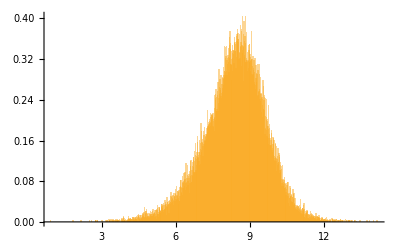

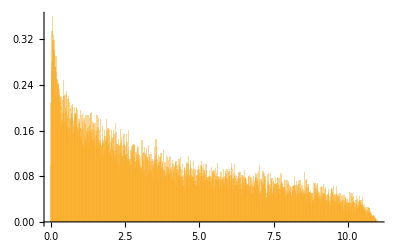

```mathematica
Histogram[mCPeta,1000,"PDF"]
Histogram[mCPE,1000,"PDF"]
```

```mathematica
Length[eveLLtestdata]
```

50001